# Counter passing distribution function notebook

Reset all parameters before running

```mathematica
ClearAll["Global`*"]
```

First/second derivative of slowing down function wrt energy

```mathematica
D[Exp[-(mub0/ee-Λ0)^2/ΔΛ^2]*1/(ee^(3/2)+eec^(3/2)),ee];
```

```mathematica
D[D[Exp[-(mub0/ee-Λ0)^2/ΔΛ^2]*1/(ee^(3/2)+eec^(3/2)),ee],ee]//FullSimplify;
```

Define constants and also calculate critical beam energy & GAM frequency

```mathematica
m=2.014*1.66*10^-27;mb=m;me=9.109*10^-31; (*Bulk plasma, beam ions, electron mass*)
B0=2.2;R0=1.67;a=0.67;
ei = 1.6*10^-19;zf=1; (*Ion charge number*)
Λ0=0.53;ΔΛ=0.2;Δψ=0.5;ψ1=0.11811329814917339; (*Pitch angle & pphi values*)
eebeam = 75*10^3 ei; (*Beam energy 75keV*)
c=(3 π^(1/2)*zf*mb^(3/2))/(4*me^(1/2)*m);
eec = Te0 * c^(2/3); (*Critical beam energy*)
Te0=2.8787878787878785*1000*ei;
Ti0=Te0;
(* From Fu *)
η=0.63/1.42;
Z=1;

q=3; κ=1;
fG=κ(√(2*(Te0+7/4Ti0)/m))/(2π R0) (*GAM freq*)
wb0=√(2/m(1-Λ0)eebeam)/(q R0) ;(*ω at resonance*)
wb0/Z/2/π
tfact = 1.2576923076923077; (*ti = tfact*te*)
Solve[(κ √(2*(xe+7/4xe)/m*1000*ei))/(2π R0)==wb0/Z/2/π,xe]
```

82959.5

58351.7

{{xe→1.42424}}

Normalization factor for dist fun - integrate over velocity variables y-v_⊥, x-v_(||), include Jacobian

```mathematica
cnorm = 1/NIntegrate[(2π y)/((m/2)^(3/2)(x^2+y^2)^(3/2)+eec^(3/2))Exp[(-(y^2/(x^2+y^2)-Λ0)^2)/ΔΛ^2]Boole[x^2+y^2≤ (2*eebeam)/m&&y^2/(x^2+y^2)<1],{x,-√((2*eebeam)/m),0},{y,0,√((2*eebeam)/m)}]
```

1.238×10^-40

Subbing in values for f, f’ & f’’ for debugging purposes

```mathematica
eesub=26.774878487*1000*ei;
mub0sub = 10*1000*ei;
pphisub = -1.12903*ei*ψ1;
Exp[-(mub0/ee-Λ0)^2/ΔΛ^2]*cnorm/(ee^(3/2)+eec^(3/2))*Exp[pphi/(ei*Δψ*ψ1)]/.{ee->eesub,mub0->10*10^3*1.60*10^-19,pphi->pphisub};
D[Exp[-(mub0/ee-Λ0)^2/ΔΛ^2]*cnorm/(ee^(3/2)+eec^(3/2))*Exp[pphi/(ei*Δψ*ψ1)],ee]/.{ee->eesub,mub0->10*10^3*1.60*10^-19,pphi->pphisub};
D[D[Exp[-(mub0/ee-Λ0)^2/ΔΛ^2]*cnorm/(ee^(3/2)+eec^(3/2))*Exp[pphi/(ei*Δψ*ψ1)],ee],ee]/.{ee->eesub,mub0->10*10^3*1.60*10^-19,pphi->pphisub};
```

Attempt to include r & θ dependence when calculating norm. factor

```mathematica
(* NIntegrate[(2π y)/((m/2)^(3/2)(x^2+y^2)^(3/2)+eec^(3/2))Exp[(-(y^2/(x^2+y^2)*1/(1-r/R0 Cos[θ])-Λ0)^2)/ΔΛ^2]Boole[x^2+y^2≤ (2*eebeam)/m&&y^2/(x^2+y^2)<1-r/R0 Cos[θ]],{x,-√((2*eebeam)/m),0},{y,0,√((2*eebeam)/m)},{r,0,a},{θ,0,2π}] *)
```

Resonance map - plot f and f’ over E & μB_0, highlight line where ω=(v_(||))/qR_0. See where line coincides with positive f’

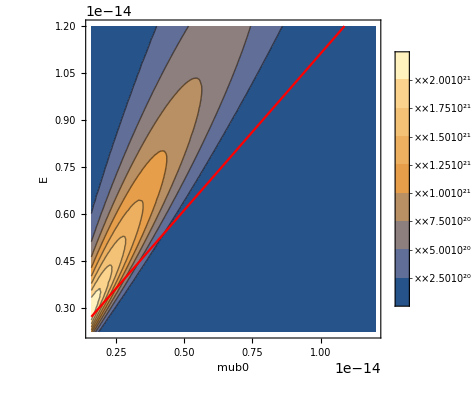

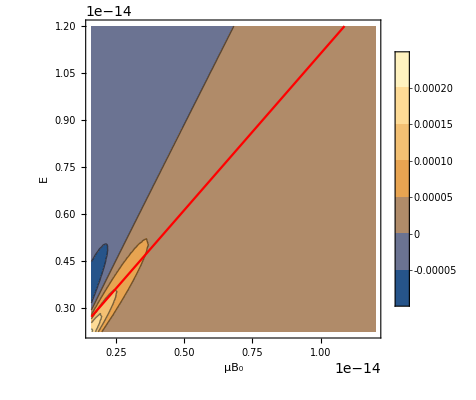

```mathematica
cp1 = ContourPlot[{Exp[-(mub0/ee-Λ0)^2/ΔΛ^2]*1/(ee^(3/2)+eec^(3/2))},{mub0,10*1000*ei,eebeam},{ee,14*1000*ei,eebeam},PlotPoints->10,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"mub0","E"}]; (*f plot*)
lp1 = Plot[mub0+η^2(1-Λ0)*eebeam,{mub0,10*1000*ei,eebeam},PlotRange->{14*1000*ei,eebeam},PlotStyle->{Red,Thick}]; (*Resonance line*)
Show[cp1,lp1]
cp2 = ContourPlot[(-(3 ⅇ^(-(mub0/ee-Λ0)^2/ΔΛ^2) √ee)/(2 (ee^(3/2)+eec^(3/2))^2)+(2 ⅇ^(-(mub0/ee-Λ0)^2/ΔΛ^2) mub0 (mub0/ee-Λ0))/(ee^2 (ee^(3/2)+eec^(3/2)) ΔΛ^2))*cnorm,{mub0,10*1000*ei,eebeam},{ee,14*1000*ei,eebeam},PlotPoints->10,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"μB_0","E"}];(*f' plot*)
Show[cp2,lp1]
```

Analytic following Cao 2015

```mathematica
D1=(2-Λ0)(5*Λ0-2)/(2(1-Λ0)^(5/2));D2=Λ0*(2-Λ0)^2/(1-Λ0)^(5/2); (*Constants*)
(*c0=Γ/(4π γc);n0=1;ωb=1/(q*R0)√((2(eebeam - mub0))/m);*)
fb=1.42*fG (*Bounce frequency - set to 1.4fG from Fu 2008*)
c0=0.001;n0=0.1; (*Not sure what these should be. Only ratio matters, just guess values*)
sol =f/.FindRoot[-1+fG^2/f^2+π/(√2)B0*q^2*c0/n0*(D1*Log[1-(fb/f)^2]+D2*(1/(1-(fb/f)^2)-1))==0,{f,0.5*fb}](*Predicted EGAM values*)
sol*2π
```

83298.8

29671.+13047.5 ⅈ

186428.+81979.6 ⅈ

Calculating Y = fast ion pressure / thermal plasma pressure, defined in Fu 2008
P_(||h)=∫dE dP_ϕ dμ f(E,μ,P_ϕ) [E-μB_0] , P_(⊥h)=∫dE dP_ϕ dμ f(E,μ,P_ϕ) μB_0 → P_h=∫dE dP_ϕ dμ f(E,μ,P_ϕ) E
P_th=nk_B T

```mathematica
qprof[r_]:= 4 r^2-3.2r+4.16;
Integrate[(B0 r)/qprof[r],r];
```

```mathematica
(* i1[mub0_,ee_?NumericQ]:=i1[mub0,ee]=NIntegrate[r*Exp[-(mub0/ee-Λ0)^2/ΔΛ^2]*cnorm/(ee^(3/2)+eec^(3/2))*Exp[((-B0 ei)/(2q)r^2+m R0 √(2/m(ee-mub0)))/(ei*Δψ*ψ1)]*(2 B0 π)/m^2*((√2 √(ee-mub0))/(√m))^-1,{r,0,a}];
i2[mub0_?NumericQ]:=i2[mub0]= NIntegrate[i1[mub0,ee],{ee,mub0,eebeam}]; *)
```

```mathematica
i3[mub0_?NumericQ]:=i3[mub0]=NIntegrate[Exp[-(mub0/ee-Λ0)^2/ΔΛ^2]*cnorm/(ee^(3/2)+eec^(3/2))*Exp[(m R0 √(2/m(ee-mub0)))/(ei*Δψ*ψ1)]*(2 B0 π)/m^2*((√2 √(ee-mub0))/(√m))^-1,{ee,mub0,eebeam}];
int1 =NIntegrate[i3[mub0],{mub0, 10*1000*ei,eebeam}];
int2 = NIntegrate[r*Exp[(-B0 r^2/(2q))/(Δψ*ψ1)],{r,0,a}];
```

```mathematica
nfratio=0.1;γ=7/4;
Ph = nfratio*5.9235296295818867*10^-15
vol = π a^2*2π R0
Pth = Ti0*vol

Y = Ph/(Pth*2*γ)
```

5.92353×10^-16

14.7978

3.40796×10^-15

0.0496613

```mathematica
(π B0)/m^(3/2)√(2/(ee-mub0))*Exp[-(mub0/ee-Λ0)^2/ΔΛ^2]*1/(ee^(3/2)+eec^(3/2))/.{ee->101*1000*ei,mub0->70*10^3*1.60*10^-19}
```

1.51697×10^68

```mathematica
NIntegrate[(2π y)/((m/2)^(3/2)(x^2+y^2)^(3/2)+eec^(3/2))Exp[(-(y^2/(x^2+y^2)-0.8)^2)/0.2^2]Boole[x^2+y^2≤ (2*eebeam)/m&&y^2/(x^2+y^2)<1],{x,-√((2*eebeam)/m),0},{y,0,√((2*eebeam)/m)}]
```

2.34684×10^40

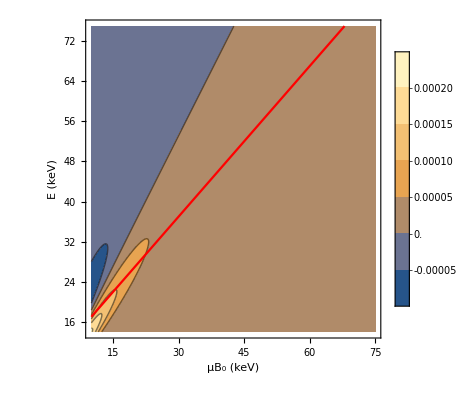

```mathematica
lp3 = Plot[mub0+η^2(1-Λ0)*eebeam/1000/ei,{mub0,10,75},PlotRange->{14,75},PlotStyle->{Red,Thick}]; (*Resonance line*)
cp3 = ContourPlot[(-(3 ⅇ^(-(mub0/ee-Λ0)^2/ΔΛ^2) √(ee*1000*ei))/(2 ((ee*1000*ei)^(3/2)+eec^(3/2))^2)+(2 ⅇ^(-(mub0/ee-Λ0)^2/ΔΛ^2) mub0*1000*ei (mub0/ee-Λ0))/((ee*1000*ei)^2 ((ee*1000*ei)^(3/2)+eec^(3/2)) ΔΛ^2))*cnorm,{mub0,10,75},{ee,14,75},PlotPoints->100,PlotRange->All,PlotLegends->BarLegend[Automatic,LegendFunction->(ScientificForm[#//N]&)],FrameLabel->{"μB_0 (keV)","E (keV)"}];(*f' plot*)
Show[cp3,lp3]
```